```mathematica
f[x_]:=(x^2-36)^2/10000
```

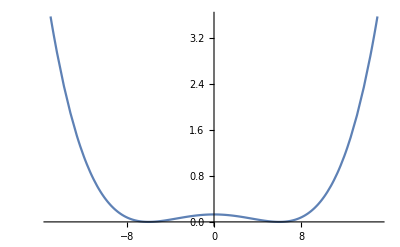

```mathematica
Plot[f[x],{x,-15,15}]
```

```mathematica
(* approximate with Gaussian basis functions *)
```

```mathematica
ξ[j_,h_]:=j h
```

```mathematica
ϕ[x_,j_,h_,α_]:=Exp[-α (x - ξ[j,h])^2]
```

```mathematica
(* Suppose j = -J, -J+1, ..., J *)
```

```mathematica
(* Suppose we want J h = L, then h = L/J *)
```

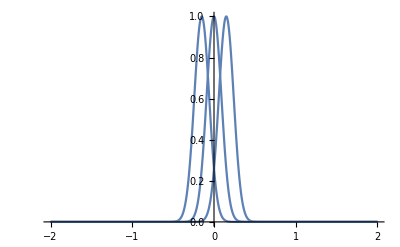

```mathematica
bigL=15;
bigJ=100;
myh=bigL/bigJ;
myalpha= 60.0 (*4.0 Log[2]/myh^2*); 
Plot[Table[ϕ[x,k,bigL/bigJ,myalpha],{k,-1,1}],{x,-2,2},PlotRange->All]
```

```mathematica
gmat=Table[ϕ[ξ[j,bigL/bigJ],k,bigL/bigJ,myalpha],{j,-bigJ,bigJ},{k,-bigJ,bigJ}];
```

General::munfl: Exp[-714.15] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-777.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-843.75] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Dimensions[gmat]
```

{201,201}

```mathematica
fvec=Table[f[ξ[j,bigL/bigJ]],{j,-bigJ,bigJ}];
```

```mathematica
Dimensions[fvec]
```

{201}

```mathematica
β = LinearSolve[gmat, fvec];
```

```mathematica
ClearAll[fapprox]
```

```mathematica
fapprox[x_]:=Sum[β[[j+bigJ+1]] ϕ[x,j,bigL/bigJ,myalpha],{j,-bigJ,bigJ}];
```

General::munfl: Exp[-713.896] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-777.335] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-843.474] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

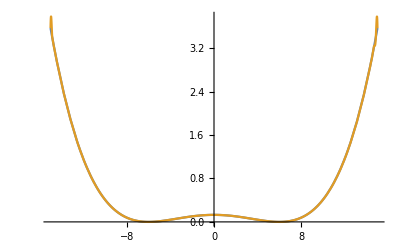

```mathematica
Plot[{f[x],fapprox[x]},{x,-15,15},PlotRange->All]
```

```mathematica
(* L2 error *)
Sqrt[NIntegrate[(f[x]-fapprox[x])^2,{x,-bigL,bigL}]]
```

0.380913

```mathematica
(* one function that computes the L2 error when we use a certain number of basis functions *)
```

```mathematica
ClearAll[myh,myalpha,k,gmat,fvec,β,fapprox]
```

```mathematica
error[thisJ_]:=Block[{myh,myalpha,k,gmat,fvec,β,fapprox},
myh=bigL/thisJ;
myalpha=1.0; (* 4.0 Log[2]/myh^2;  *)
gmat=Table[ϕ[ξ[j,myh],k,myh,myalpha],{j,-thisJ,thisJ},{k,-thisJ,thisJ}];
fvec=Table[f[ξ[j,myh]],{j,-thisJ,thisJ}];
β = LinearSolve[gmat, fvec];
fapprox[x_]:=Sum[β[[j+thisJ+1]] ϕ[x,j,myh,myalpha],{j,-thisJ,thisJ}];
{Sqrt[NIntegrate[(f[x]-fapprox[x])^2,{x,-bigL,bigL}]],
Plot[{f[x],fapprox[x]},{x,-bigL,bigL},PlotRange->All,PlotPoints->100]}
]
```

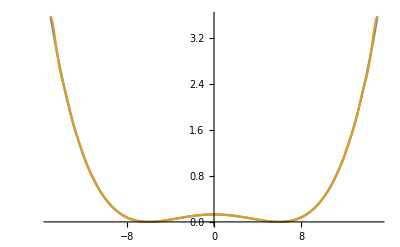
{0.0883611,-Graphics-}

```mathematica
error[25]
```

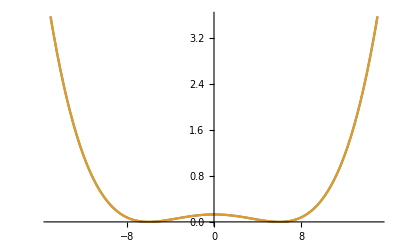
{0.000549996,-Graphics-}

```mathematica
error[50]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-5.74265}. NIntegrate obtained 1.14283×10^-11 and 5.19819×10^-13 for the integral and error estimates.

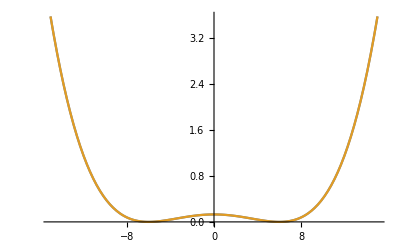
{3.38057×10^-6,-Graphics-}

```mathematica
error[100]
```